```mathematica
i10={{10.600,10.000,{42.31,0.68}},{10.740,10.000,{44.34,0.67}},{10.880,10.000,{46.28,0.75}},{11.020,10.000,{47.26,0.76}},{11.160,10.000,{50.13,0.83}},{11.300,10.000,{50.60,0.81}},{11.440,10.000,{52.72,0.88}},{11.580,10.000,{55.19,0.91}},{11.720,10.000,{57.62,0.97}},{11.860,10.000,{56.97,1.01}},{12.000,10.000,{61.09,1.04}}};
```

```mathematica
SolveNi[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
nc=Min[ii[[All,2]]];
Assert[nc==Max[ii[[All,2]]]];
data={#[[1]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
ni=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[1]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Ni","Ions"},
PlotLabel->StringTemplate["Nc = `1`, Ni = `2` ± `3`"][nc,ni,err]],
Plot[lf[x],{x,Min[ii[[All,1]]-1],Max[ii[[All,1]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{ni,60},{ni,51}}],Line[{{ni-err,50},{ni+err,50}}]}
]];
{nc,Around[ni,err]}
]
```

```mathematica
SolveNc[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
ni=Min[ii[[All,1]]];
Assert[ni==Max[ii[[All,1]]]];
data={#[[2]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
nc=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[2]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Nc","Ions"},
PlotLabel->StringTemplate["Ni = `1`, Nc = `2` ± `3`"][ni,nc,err]],
Plot[lf[x],{x,Min[ii[[All,2]]-1],Max[ii[[All,2]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{nc,60},{nc,51}}],Line[{{nc-err,50},{nc+err,50}}]}
]];
{Around[nc,err],ni}
]
```

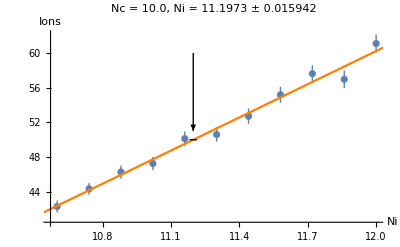

{10.,11.1970.016}

```mathematica
SolveNi[i10]
```

```mathematica
i10a={{10.500,10.000,{40.15,0.63}},{10.650,10.000,{42.80,0.65}},{10.800,10.000,{43.74,0.69}},{10.950,10.000,{45.34,0.71}},{11.100,10.000,{48.42,0.77}},{11.250,10.000,{50.02,0.82}},{11.400,10.000,{51.78,0.87}},{11.550,10.000,{53.95,0.93}},{11.700,10.000,{55.20,0.92}},{11.850,10.000,{58.40,1.00}},{12.000,10.000,{60.31,1.07}}};
```

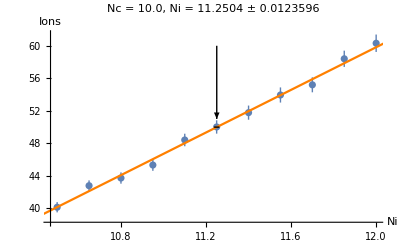

{10.,11.2500.012}

```mathematica
SolveNi[i10a]
```

```mathematica
i10b={{10.500,10.000,{40.32,0.61}},{10.650,10.000,{42.52,0.68}},{10.800,10.000,{44.35,0.70}},{10.950,10.000,{45.42,0.72}},{11.100,10.000,{47.62,0.77}},{11.250,10.000,{50.58,0.82}},{11.400,10.000,{52.72,0.87}},{11.550,10.000,{54.73,0.87}},{11.700,10.000,{56.00,0.94}},{11.850,10.000,{58.75,1.01}},{12.000,10.000,{60.52,1.03}}};
```

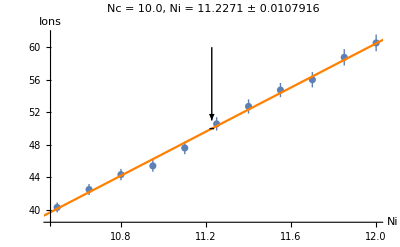

{10.,11.2270.011}

```mathematica
SolveNi[i10b]
```

```mathematica
i10c={{10.500,10.000,{39.65,0.59}},{10.650,10.000,{42.32,0.67}},{10.800,10.000,{45.08,0.68}},{10.950,10.000,{45.93,0.75}},{11.100,10.000,{46.65,0.76}},{11.250,10.000,{51.38,0.83}},{11.400,10.000,{52.72,0.89}},{11.550,10.000,{55.55,0.90}},{11.700,10.000,{55.37,0.94}},{11.850,10.000,{57.18,0.98}},{12.000,10.000,{60.56,1.07}}};
```

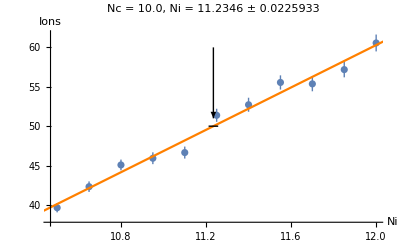

{10.,11.2350.023}

```mathematica
SolveNi[i10c]
```

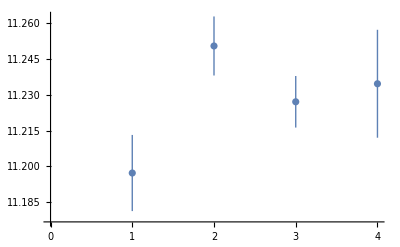

```mathematica
ListPlot[{11.1970.016,11.2500.012,11.2270.011,11.2350.023}]
```

```mathematica
StandardDeviation[#[[1]]&/@{11.1970.016,11.2500.012,11.2270.011,11.2350.023}]
```

0.0223038

```mathematica
Mean[{11.1970.016,11.2500.012,11.2270.011,11.2350.023}]
```

11.2270.008

```mathematica
paschenCurve={{10,%}}
```

{{10,11.2270.008}}

```mathematica
10^(1/4)//N
```

1.77828

```mathematica
10^(1/2)//N
```

3.16228

```mathematica
10^(3/4)//N
```

5.62341

```mathematica
i17={{10.500,17.800,{40.42,0.43}},{10.600,17.800,{41.11,0.44}},{10.700,17.800,{42.85,0.47}},{10.800,17.800,{45.43,0.49}},{10.900,17.800,{47.08,0.53}},{11.000,17.800,{49.55,0.55}},{11.100,17.800,{51.19,0.59}},{11.200,17.800,{53.55,0.63}},{11.300,17.800,{56.35,0.65}},{11.400,17.800,{57.41,0.67}},{11.500,17.800,{59.47,0.72}}};
```

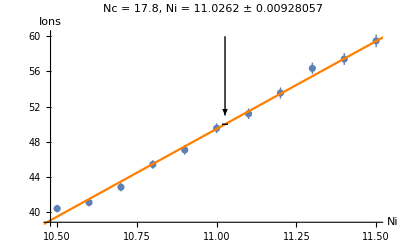

{17.8,11.0260.009}

```mathematica
SolveNi[i17]
```

```mathematica
i31={{12.200,31.600,{40.50,0.38}},{12.300,31.600,{42.72,0.42}},{12.400,31.600,{44.39,0.44}},{12.500,31.600,{46.45,0.45}},{12.600,31.600,{49.07,0.50}},{12.700,31.600,{51.68,0.50}},{12.800,31.600,{52.99,0.51}},{12.900,31.600,{55.78,0.53}},{13.000,31.600,{57.76,0.56}},{13.100,31.600,{61.34,0.58}},{13.200,31.600,{63.22,0.63}}};
```

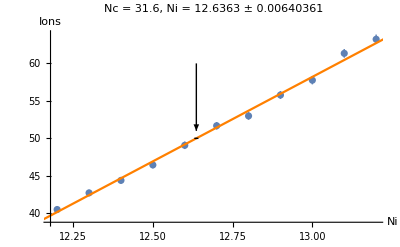

{31.6,12.6360.006}

```mathematica
SolveNi[i31]
```

```mathematica
i56={{15.000,56.200,{37.68,1.33}},{15.100,56.200,{41.29,1.00}},{15.200,56.200,{42.95,1.30}},{15.300,56.200,{42.84,1.39}},{15.400,56.200,{46.17,1.64}},{15.500,56.200,{48.98,1.46}},{15.600,56.200,{51.11,1.60}},{15.700,56.200,{53.34,1.63}},{15.800,56.200,{54.30,1.45}},{15.900,56.200,{55.89,1.72}},{16.000,56.200,{63.02,2.28}}};
```

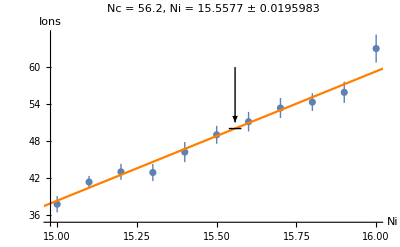

{56.2,15.5580.020}

```mathematica
SolveNi[i56]
```

```mathematica
i100={{20.000,100.000,{42.46,1.74}},{20.080,100.000,{46.70,1.64}},{20.160,100.000,{45.21,1.67}},{20.240,100.000,{47.63,1.77}},{20.320,100.000,{50.14,1.85}},{20.400,100.000,{50.92,1.73}},{20.480,100.000,{51.94,1.86}},{20.560,100.000,{51.26,1.86}},{20.640,100.000,{54.84,1.90}},{20.720,100.000,{59.09,2.09}},{20.800,100.000,{61.71,2.21}}}
```

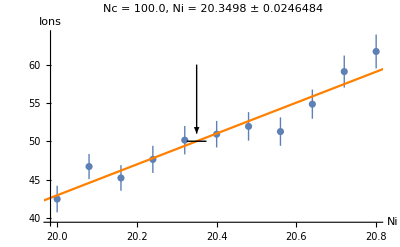

{100.,20.3500.025}

```mathematica
SolveNi[i100]
```

```mathematica
i178={{27.200,178.000,{43.43,1.87}},{27.310,178.000,{39.55,1.88}},{27.420,178.000,{42.26,1.65}},{27.530,178.000,{44.76,1.89}},{27.640,178.000,{51.04,2.24}},{27.750,178.000,{49.87,1.87}},{27.860,178.000,{46.20,2.58}},{27.970,178.000,{53.10,2.45}},{28.080,178.000,{54.84,2.31}},{28.190,178.000,{55.49,2.69}},{28.300,178.000,{59.87,2.59}}};
```

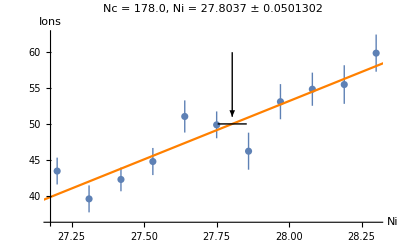

{178.,27.800.05}

```mathematica
SolveNi[i178]
```

```mathematica
i316={{38.700,316.000,{39.68,2.29}},{38.880,316.000,{39.96,2.13}},{39.060,316.000,{44.03,2.38}},{39.240,316.000,{49.11,2.54}},{39.420,316.000,{49.47,2.71}},{39.600,316.000,{52.59,3.18}},{39.780,316.000,{55.02,3.09}},{39.960,316.000,{52.40,3.05}},{40.140,316.000,{61.44,3.66}},{40.320,316.000,{63.66,3.30}},{40.500,316.000,{66.83,3.34}}};
```

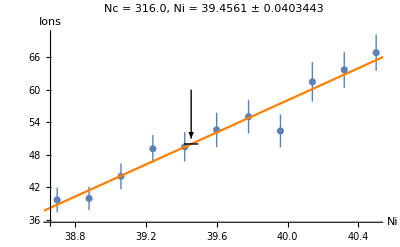

{316.,39.460.04}

```mathematica
SolveNi[i316]
```

```mathematica
i562={{57.000,562.000,{36.55,1.67}},{57.200,562.000,{43.88,2.07}},{57.400,562.000,{44.70,1.90}},{57.600,562.000,{48.23,2.05}},{57.800,562.000,{47.06,1.97}},{58.000,562.000,{50.70,2.35}},{58.200,562.000,{48.77,2.12}},{58.400,562.000,{58.69,2.56}},{58.600,562.000,{53.69,2.43}},{58.800,562.000,{60.85,2.64}},{59.000,562.000,{61.37,2.58}}};
```

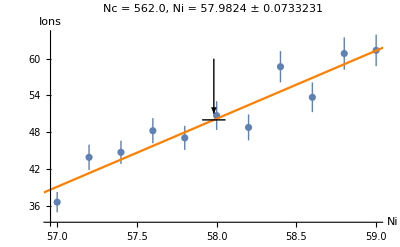

{562.,57.980.07}

```mathematica
SolveNi[i562]
```

```mathematica
i1000={{86.000,1000.000,{38.96,1.40}},{86.300,1000.000,{43.65,1.49}},{86.600,1000.000,{41.02,1.46}},{86.900,1000.000,{42.69,1.59}},{87.200,1000.000,{44.20,1.47}},{87.500,1000.000,{48.43,1.78}},{87.800,1000.000,{47.48,1.59}},{88.100,1000.000,{53.02,1.91}},{88.400,1000.000,{54.81,2.04}},{88.700,1000.000,{61.15,2.06}},{89.000,1000.000,{65.17,2.26}}};
```

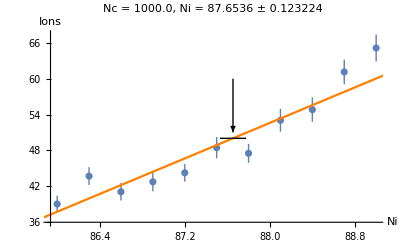

{1000.,87.650.12}

```mathematica
SolveNi[i1000]
```

```mathematica
AppendTo[paschenCurve,%]
```

{{4.0320.006,100.},{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025},{178.,27.800.05},{316.,39.460.04},{562.,57.980.07},{1000.,87.650.12}}

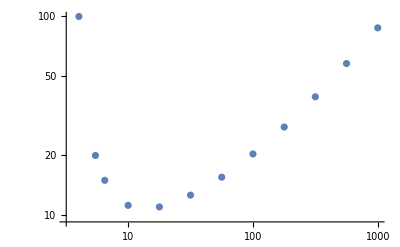

```mathematica
ListLogLogPlot[paschenCurve]
```

```mathematica
c20={{20.000,5.100,{38.77,1.00}},{20.000,5.170,{43.11,1.15}},{20.000,5.240,{46.82,1.26}},{20.000,5.310,{44.31,1.21}},{20.000,5.380,{48.58,1.29}},{20.000,5.450,{48.92,1.31}},{20.000,5.520,{50.99,1.34}},{20.000,5.590,{54.03,1.42}},{20.000,5.660,{55.08,1.36}},{20.000,5.730,{56.85,1.45}},{20.000,5.800,{57.90,1.51}}};
```

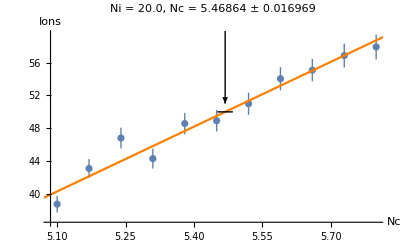

{5.4690.017,20.}

```mathematica
SolveNc[c20]
```

```mathematica
c15={{15.000,6.000,{42.47,1.03}},{15.000,6.100,{43.03,1.05}},{15.000,6.200,{46.27,1.08}},{15.000,6.300,{45.91,1.04}},{15.000,6.400,{47.91,1.14}},{15.000,6.500,{49.66,1.16}},{15.000,6.600,{50.79,1.17}},{15.000,6.700,{52.53,1.22}},{15.000,6.800,{56.79,1.32}},{15.000,6.900,{56.19,1.31}},{15.000,7.000,{60.16,1.41}}};
```

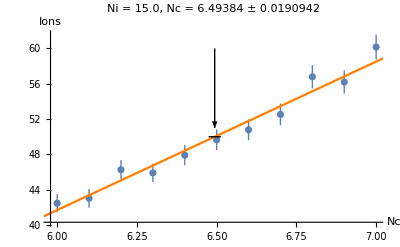

{6.4940.019,15.}

```mathematica
SolveNc[c15]
```

```mathematica
c100={{100.000,3.800,{38.88,0.38}},{100.000,3.850,{42.33,0.42}},{100.000,3.900,{43.87,0.44}},{100.000,3.950,{46.48,0.47}},{100.000,4.000,{47.52,0.47}},{100.000,4.050,{50.80,0.50}},{100.000,4.100,{51.35,0.52}},{100.000,4.150,{55.47,0.55}},{100.000,4.200,{58.75,0.59}},{100.000,4.250,{60.47,0.60}},{100.000,4.300,{64.14,0.65}}};
```

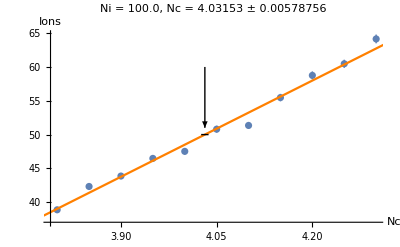

{4.0320.006,100.}

```mathematica
SolveNc[c100]
```

```mathematica
c45={{45.000,4.100,{40.29,1.24}},{45.000,4.160,{42.08,1.30}},{45.000,4.220,{42.88,1.34}},{45.000,4.280,{46.62,1.41}},{45.000,4.340,{49.88,1.48}},{45.000,4.400,{49.81,1.52}},{45.000,4.460,{49.36,1.50}},{45.000,4.520,{56.14,1.66}},{45.000,4.580,{58.82,1.69}},{45.000,4.640,{61.17,1.87}},{45.000,4.700,{62.87,1.79}}};
```

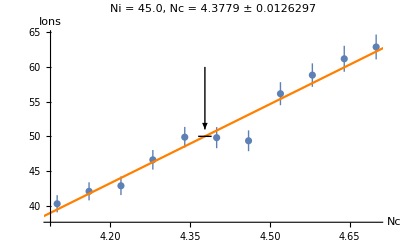

{4.3780.013,45.}

```mathematica
SolveNc[c45]
```

```mathematica
PrependTo[paschenCurve,%]
```

{{4.3780.013,45.},{4.0320.006,100.},{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025},{178.,27.800.05},{316.,39.460.04},{562.,57.980.07},{1000.,87.650.12}}

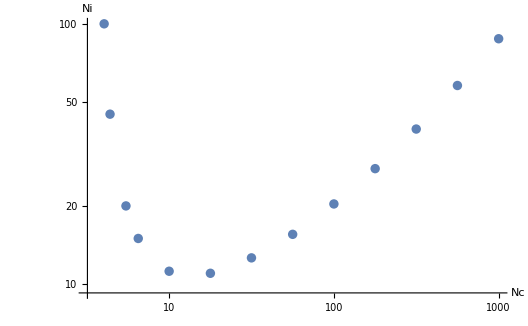

```mathematica
ListLogLogPlot[paschenCurve,AxesLabel->{"Nc","Ni"}]
```

```mathematica
Sort[paschenCurve,#1[[1]]<#2[[1]]&]
```

{{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}

```mathematica
cWB={{100,0.5,{1.73,.07}},{100,1.5,{4.43,0.25}},{100,2.5,{12.2,0.8}},{100,3.5,{28.8,1.8}},{100,4.5,{67,4}},{100,5.5,{202,14}}};
```

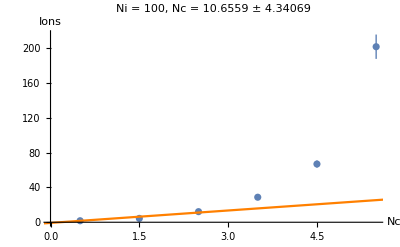

{11.4.,100}

```mathematica
SolveNc[cWB]
```

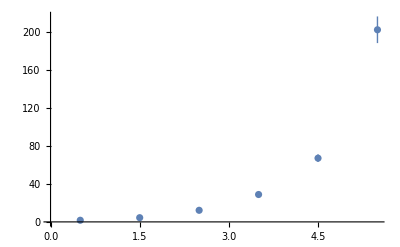

```mathematica
ListPlot[{#[[2]],Around[#[[3,1]],#[[3,2]]]}&/@cWB]
```

```mathematica
{#[[2]],#[[3]]}&/@cWB
```

```mathematica
{{0.5,{1.73,0.07}},{1.5,{4.43,0.25}},{2.5,{28.8,1.8}},{4.5,{67,4}},{5.5,{202,14}}}
```

{{0.5,{1.73,0.07}},{1.5,{4.43,0.25}},{2.5,{28.8,1.8}},{4.5,{67,4}},{5.5,{202,14}}}

```mathematica
dataWB={#[[2]],#[[3,1]]}&/@cWB
```

{{0.5,1.73},{1.5,4.43},{2.5,12.2},{3.5,28.8},{4.5,67},{5.5,202}}

```mathematica
weightsWB=(#[[3,2]])^-2&/@cWB
```

{204.082,16.,1.5625,0.308642,1/16,1/196}

```mathematica
lfWB=LinearModelFit[dataWB,{x,x^2},x,Weights->weightsWB]
```

FittedModel[3.73826-6.06152 x+4.14995 x^2]

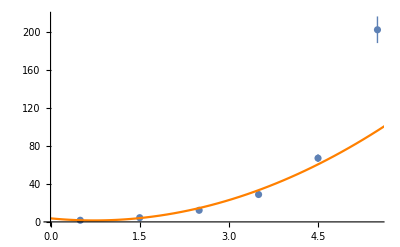

```mathematica
Show[ListPlot[{#[[2]],Around[#[[3,1]],#[[3,2]]]}&/@cWB],
Plot[lfWB[x],{x,0,6},PlotStyle->Orange]]
```

```mathematica
vals={{3,Around[18.5,1.1]},{3.5,Around[31.2,1.8]},{4,Around[47.5,2.7]},{4.5,Around[79,4]},{5,Around[121,7]}}
```

{{3,18.51.1},{3.5,31.21.8},{4,47.52.7},{4.5,79.4.},{5,121.7.}}

```mathematica
nlf=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@vals,p1 Exp[p2 x]+p3,{p1,p2,p3},x,Weights->1/(#[[2,2]]&/@vals)^2]
```

FittedModel[-3.28487+1.60157 ⅇ^(0.871451 x)]

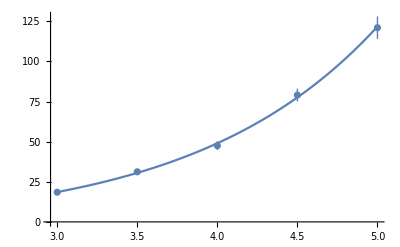

```mathematica
Show[ListPlot[vals],Plot[nlf[x],{x,3,5}]]
```

```mathematica
nlf2=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@vals,p1 Exp[p2 x]+p3,{p1,p2,p3},x,Weights->1/(#[[2,2]]&/@vals)^2,Method->NMinimize]
```

FittedModel[-3.28496+1.60159 ⅇ^(0.871449 x)]

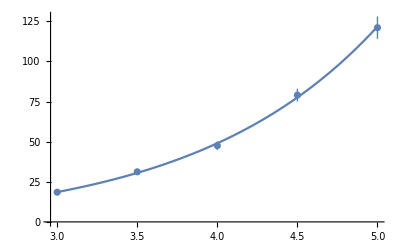

```mathematica
Show[ListPlot[vals],Plot[nlf2[x],{x,3,5}]]
```

```mathematica
Total[(nlf2["FitResiduals"]/errs)^2]
```

0.593408

```mathematica
nlf1=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@vals,p1 Exp[p2 x]+p3,{p1,p2,p3},x]
```

FittedModel[-4.4034+1.7674 ⅇ^(0.852934 x)]

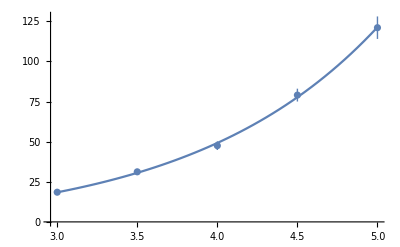

```mathematica
Show[ListPlot[vals],Plot[nlf1[x],{x,3,5}]]
```

```mathematica
nlf1[5]
```

121.332

```mathematica
nlf["StandardizedResiduals"]
```

{-0.59783,0.886967,-1.40878,0.833272,-0.41863}

```mathematica
nlf["FitResiduals"]
```

{-0.0900204,0.664451,-1.50434,1.44135,-0.706005}

```mathematica
nlf1["StandardizedResiduals"]
```

{0.0882863,0.475561,-1.40996,1.18865,-1.01329}

```mathematica
nlf1["FitResiduals"]
```

{0.0679514,0.623233,-1.68049,1.32167,-0.332366}

```mathematica
errs=#[[2,2]]&/@vals
```

{1.1,1.8,2.7,4.,7.}

```mathematica
cs1=Total[(nlf1["FitResiduals"]/errs)^2]
```

0.622512

```mathematica
cs=Total[(nlf["FitResiduals"]/errs)^2]
```

0.593408

```mathematica
Variance[%]
```

1.1429

```mathematica
nlf[5]
```

121.706

```mathematica
1/(#[[2,2]]&/@vals)^2
```

{0.826446,0.308642,0.137174,0.0625,0.0204082}

```mathematica
Around[124,8]/Around[75,4]
```

1.650.14

```mathematica
Around[121,7]/Around[79,4]
```

1.530.12

```mathematica
vals
```

{{3,18.51.1},{3.5,31.21.8},{4,47.52.7},{4.5,79.4.},{5,121.7.}}

```mathematica
vals={{3,18.51.1},{3.5,31.21.8},{4,47.52.7},{4.5,79.4.},{5,121.7.}};
```

```mathematica
cwVals1={{100.000,3.000,{19.08,1.22}},{100.000,3.500,{33.30,1.80}},{100.000,4.000,{46.62,2.58}},{100.000,4.500,{67.71,3.92}},{100.000,5.000,{123.56,7.04}}};
```

```mathematica
cwNlf1=NonlinearModelFit[{#[[2]],#[[3,1]]}&/@cwVals1,p1 Exp[p2 x]+p3,{p1,p2,p3},x]
```

FittedModel[13.9946+0.179058 ⅇ^(1.28162 x)]

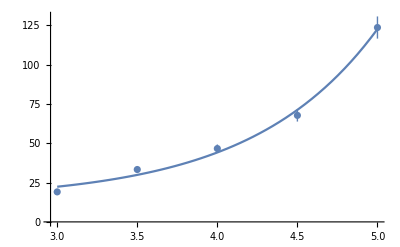

```mathematica
Show[ListPlot[{#[[2]],Around[#[[3,1]],#[[3,2]]]}&/@cwVals1],Plot[cwNlf1[x],{x,3,5}]]
```

```mathematica
cwCs1=Total[(cwNlf1["FitResiduals"]/(#[[3,2]]&/@cwVals1))^2]
```

12.5973

```mathematica
ExpFitter[vals_]:=Module[{nlf,chiSquare},
nlf=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@vals,p1 Exp[p2 x]+p3,{p1,p2,p3},x,Weights->((1/(#[[2,2]])^2)&/@vals)];
Print[nlf];
Print[Show[ListPlot[{#[[1]],Around[#[[2,1]],#[[2,2]]]}&/@vals],Plot[nlf[x],{x,3,5}]]];
chiSquare=Total[(nlf["FitResiduals"]/(#[[2,2]]&/@vals))^2];
Print["Χ^2 = ",chiSquare];
nlf
];
```

```mathematica
ExpFitter[vals];
```

FittedModel[-4.4034+1.7674 ⅇ^(0.852934 x)]

-Graphics-

Χ^2 = 0.622512

```mathematica
ExpFitter[vals];
```

FittedModel[-3.28487+1.60157 ⅇ^(0.871451 x)]

-Graphics-

Χ^2 = 0.593408

```mathematica
ExpFitter[cwVals1[[All,2;;3]]];
```

FittedModel[13.9946+0.179058 ⅇ^(1.28162 x)]

-Graphics-

Χ^2 = 12.5973

FittedModel[2.18802+1.08588 ⅇ^(0.930871 x)]

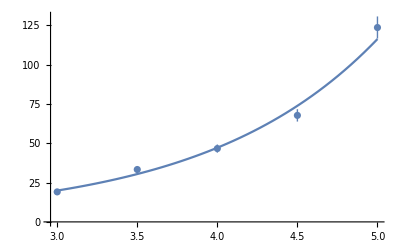

Χ^2 = 6.56454

```mathematica
ExpFitter[cwVals1[[All,2;;3]]];
```

```mathematica
cwVals1
```

{{100.,3.,{19.08,1.22}},{100.,3.5,{33.3,1.8}},{100.,4.,{46.62,2.58}},{100.,4.5,{67.71,3.92}},{100.,5.,{123.56,7.04}}}

```mathematica
cwVals1={{100.,3.,{19.08,1.22}},{100.,3.5,{33.3,1.8}},{100.,4.,{46.62,2.58}},{100.,4.5,{67.71,3.92}},{100.,5.,{123.56,7.04}}};
```

```mathematica
cwVals2={{100.000,3.000,{19.24,1.09}},{100.000,3.500,{29.72,1.75}},{100.000,4.000,{49.62,3.07}},{100.000,4.500,{82.67,4.52}},{100.000,5.000,{123.60,7.33}}};
```

FittedModel[-9.15922+2.47759 ⅇ^(0.797318 x)]

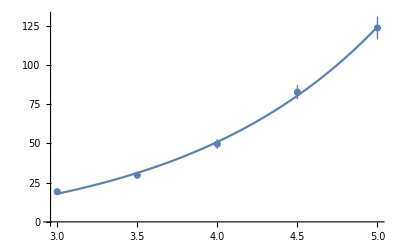

Χ^2 = 2.60626

```mathematica
ExpFitter[cwVals2[[All,2;;3]]];
```

FittedModel[-0.876236+1.21828 ⅇ^(0.930419 x)]

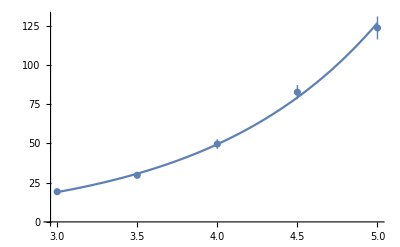

Χ^2 = 1.14659

```mathematica
ExpFitter[cwVals2[[All,2;;3]]];
```

```mathematica
cwVals3={{100.000,3.000,{17.71,1.00}},{100.000,3.500,{27.44,1.63}},{100.000,4.000,{47.25,3.16}},{100.000,4.500,{78.48,4.64}},{100.000,5.000,{129.88,7.11}}};
```

FittedModel[0.249599+0.793574 ⅇ^(1.01936 x)]

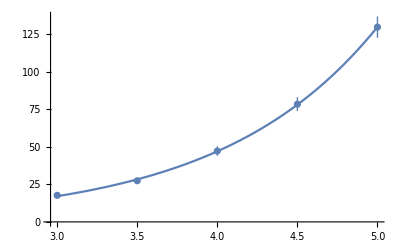

Χ^2 = 0.656764

```mathematica
ExpFitter[cwVals3[[All,2;;3]]];
```

FittedModel[2.73749+0.581989 ⅇ^(1.07906 x)]

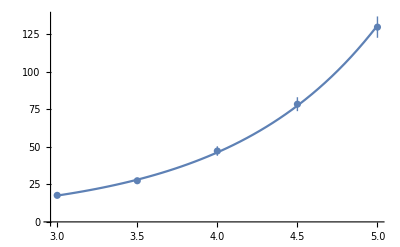

Χ^2 = 0.36799

```mathematica
ExpFitter[cwVals3[[All,2;;3]]];
```

```mathematica
cwVals4={{100.000,3.000,{17.36,0.97}},{100.000,3.500,{28.86,1.85}},{100.000,4.000,{46.99,2.40}},{100.000,4.500,{73.15,4.23}},{100.000,5.000,{123.75,7.09}}};
```

FittedModel[2.97084+0.673892 ⅇ^(1.03706 x)]

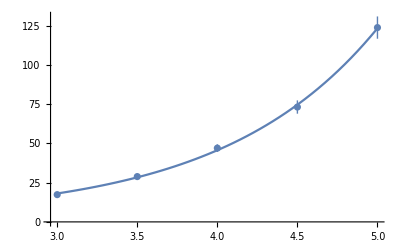

Χ^2 = 1.08932

```mathematica
ExpFitter[cwVals4[[All,2;;3]]];
```

FittedModel[-0.809542+1.04612 ⅇ^(0.952935 x)]

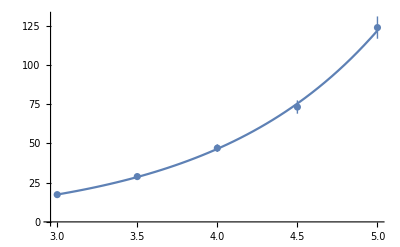

Χ^2 = 0.418961

```mathematica
ExpFitter[cwVals4[[All,2;;3]]];
```

```mathematica
cwVals5={{100.000,3.000,{18.20,0.35}},{100.000,3.500,{30.34,0.54}},{100.000,4.000,{48.22,0.88}},{100.000,4.500,{76.87,1.41}},{100.000,5.000,{121.15,2.24}}};
```

FittedModel[-2.84486+1.49279 ⅇ^(0.883906 x)]

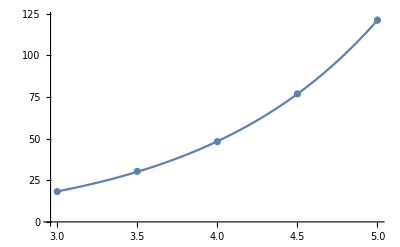

Χ^2 = 0.379302

```mathematica
ExpFitter[cwVals5[[All,2;;3]]];
```

FittedModel[-3.48668+1.58657 ⅇ^(0.872396 x)]

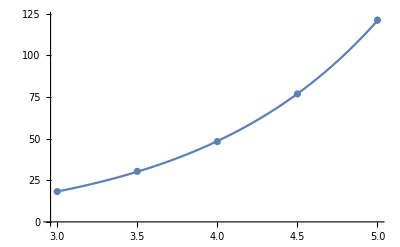

Χ^2 = 0.291491

```mathematica
ExpFitter[cwVals5[[All,2;;3]]];
```

```mathematica
cwVals6={{100.000,3.000,{18.31,0.34}},{100.000,3.500,{29.58,0.54}},{100.000,4.000,{48.75,0.87}},{100.000,4.500,{78.93,1.45}},{100.000,5.000,{122.09,2.22}}};
```

FittedModel[-5.82703+1.86682 ⅇ^(0.84582 x)]

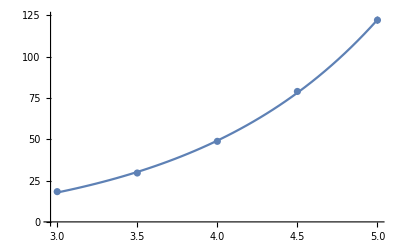

Χ^2 = 4.32461

```mathematica
ExpFitter[cwVals6[[All,2;;3]]];
```

FittedModel[-2.60814+1.39897 ⅇ^(0.899907 x)]

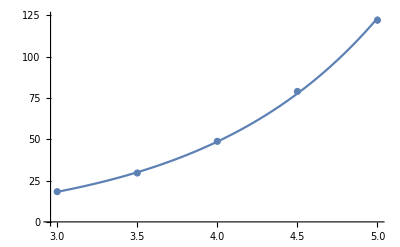

Χ^2 = 1.88155

```mathematica
ExpFitter[cwVals6[[All,2;;3]]];
```